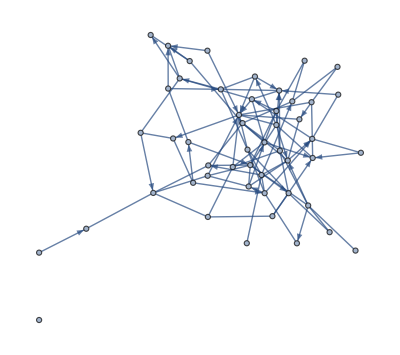

```mathematica
ResourceFunction["UndirectedGraphToMixedGraph"][RandomGraph[{50,100}],.5]
```

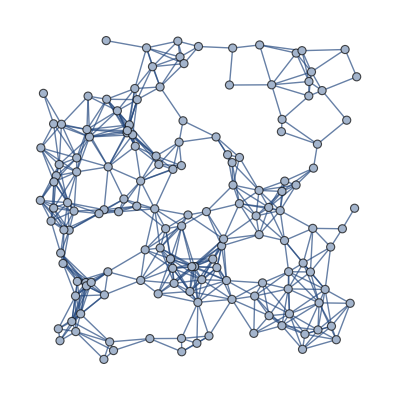

```mathematica
𝒢=Graph[First[TakeLargestBy[ConnectedGraphComponents@RandomGraph[SpatialGraphDistribution[148,E^-2]],EdgeCount,1]],ImageSize->Full]
```

```mathematica
PersistResourceFunction["UndirectedGraphToMixedGraph"]
```

Success[…]

```mathematica
FindPostmanTour[𝒢]
```

{{1<->145,145<->130,130<->124,124<->145,145<->109,109<->130,130<->84,84<->145,145<->111,111<->100,100<->125,125<->146,146<->117,117<->89,89<->123,123<->129,129<->104,104<->123,123<->87,87<->117,117<->105,105<->146,146<->107,107<->125,125<->63,63<->146,146<->32,32<->125,125<->26,26<->146,146<->20,20<->125,125<->15,15<->146,146<->7,7<->125,125<->98,98<->111,111<->98,98<->100,100<->97,97<->111,111<->62,62<->100,100<->80,80<->117,117<->112,112<->114,114<->99,99<->112,112<->95,95<->114,114<->93,93<->99,99<->95,95<->93,93<->112,112<->73,73<->97,97<->80,80<->73,73<->117,117<->78,78<->123,123<->104,104<->105,105<->89,89<->104,104<->87,87<->99,99<->78,78<->105,105<->107,107<->63,63<->117,117<->54,54<->99,99<->89,89<->129,129<->76,76<->123,123<->70,70<->129,129<->65,65<->123,123<->29,29<->129,129<->81,81<->136,136<->81,81<->90,90<->70,70<->81,81<->56,56<->70,70<->56,56<->90,90<->53,53<->81,81<->29,29<->90,90<->50,50<->56,56<->53,53<->70,70<->29,29<->66,66<->29,29<->53,53<->50,50<->127,127<->85,85<->113,113<->131,131<->46,46<->141,141<->31,31<->147,147<->42,42<->131,131<->118,118<->46,46<->42,42<->118,118<->38,38<->118,118<->30,30<->131,131<->5,5<->118,118<->113,113<->85,85<->127,127<->102,102<->5,5<->85,85<->30,30<->113,113<->38,38<->43,43<->42,42<->46,46<->5,5<->30,30<->5,5<->141,141<->121,121<->31,31<->83,83<->115,115<->138,138<->140,140<->143,143<->103,103<->140,140<->88,88<->143,143<->39,39<->140,140<->74,74<->144,144<->142,142<->128,128<->139,139<->122,122<->128,128<->122,122<->142,142<->120,120<->139,139<->92,92<->128,128<->120,120<->122,122<->144,144<->101,101<->137,137<->134,134<->101,101<->134,134<->96,96<->137,137<->86,86<->134,134<->79,79<->128,128<->96,96<->120,120<->79,79<->137,137<->75,75<->134,134<->69,69<->137,137<->67,67<->134,134<->64,64<->134,134<->61,61<->128,128<->75,75<->120,120<->92,92<->79,79<->96,96<->101,101<->75,75<->142,142<->74,74<->101,101<->69,69<->96,96<->75,75<->122,122<->61,61<->142,142<->60,60<->144,144<->23,23<->142,142<->17,17<->139,139<->82,82<->130,130<->126,126<->148,148<->51,51<->133,133<->126,126<->124,124<->84,84<->126,126<->48,48<->133,133<->49,49<->94,94<->28,28<->94,94<->67,67<->92,92<->67,67<->120,120<->61,61<->137,137<->59,59<->128,128<->23,23<->122,122<->60,60<->112,112<->68,68<->97,97<->62,62<->98,98<->26,26<->62,62<->80,80<->68,68<->73,73<->60,60<->114,114<->4,4<->93,93<->95,95<->87,87<->89,89<->78,78<->104,104<->76,76<->105,105<->65,65<->104,104<->63,63<->105,105<->41,41<->107,107<->32,32<->26,26<->100,100<->25,25<->111,111<->109,109<->84,84<->82,82<->124,124<->48,48<->148,148<->33,33<->126,126<->51,51<->130,130<->22,22<->145,145<->21,21<->130,130<->11,11<->139,139<->13,13<->128,128<->17,17<->120,120<->59,59<->96,96<->61,61<->101,101<->103,103<->138,138<->119,119<->91,91<->132,132<->106,106<->132,132<->71,71<->132,132<->110,110<->135,135<->108,108<->110,110<->106,106<->135,135<->72,72<->110,110<->55,55<->132,132<->57,57<->91,91<->71,71<->57,57<->119,119<->52,52<->138,138<->14,14<->115,115<->12,12<->138,138<->36,36<->140,140<->2,2<->138,138<->6,6<->115,115<->2,2<->143,143<->19,19<->88,88<->39,39<->19,19<->66,66<->4,4<->95,95<->54,54<->117,117<->15,15<->100,100<->9,9<->111,111<->1,1<->100,100<->20,20<->98,98<->25,25<->109,109<->22,22<->126,126<->33,33<->124,124<->51,51<->84,84<->22,22<->124,124<->21,21<->126,126<->11,11<->124,124<->48,48<->44,44<->133,133<->35,35<->48,48<->51,51<->22,22<->82,82<->17,17<->122,122<->13,13<->92,92<->75,75<->69,69<->75,75<->79,79<->86,86<->67,67<->79,79<->61,61<->75,75<->67,67<->61,61<->69,69<->74,74<->103,103<->52,52<->103,103<->36,36<->119,119<->37,37<->132,132<->24,24<->135,135<->77,77<->108,108<->106,106<->77,77<->47,47<->108,108<->72,72<->106,106<->55,55<->110,110<->18,18<->108,108<->24,24<->77,77<->64,64<->86,86<->59,59<->79,79<->13,13<->75,75<->59,59<->69,69<->52,52<->101,101<->36,36<->14,14<->36,36<->52,52<->12,12<->119,119<->40,40<->71,71<->58,58<->116,116<->58,58<->40,40<->91,91<->37,37<->64,64<->24,24<->106,106<->18,18<->132,132<->8,8<->91,91<->18,18<->77,77<->8,8<->64,64<->47,47<->86,86<->28,28<->67,67<->59,59<->134,134<->27,27<->86,86<->3,3<->77,77<->3,3<->64,64<->27,27<->37,37<->27,27<->47,47<->24,24<->37,37<->57,57<->18,18<->72,72<->55,55<->18,18<->37,37<->8,8<->27,27<->24,24<->8,8<->47,47<->3,3<->24,24<->18,18<->8,8<->57,57<->40,40<->12,12<->103,103<->2,2<->36,36<->12,12<->14,14<->83,83<->6,6<->14,14<->2,2<->12,12<->6,6<->2,2<->39,39<->19,19<->4,4<->99,99<->76,76<->87,87<->78,78<->76,76<->89,89<->63,63<->87,87<->54,54<->89,89<->65,65<->78,78<->76,76<->65,65<->63,63<->78,78<->54,54<->104,104<->41,41<->65,65<->41,41<->63,63<->15,15<->62,62<->20,20<->32,32<->15,15<->105,105<->7,7<->107,107<->34,34<->7,7<->32,32<->7,7<->63,63<->76,76<->54,54<->112,112<->45,45<->73,73<->45,45<->68,68<->60,60<->45,45<->97,97<->1,1<->109,109<->21,21<->84,84<->11,11<->82,82<->21,21<->51,51<->11,11<->22,22<->21,21<->11,11<->51,51<->33,33<->48,48<->44,44<->35,35<->49,49<->10,10<->94,94<->16,16<->28,28<->10,10<->16,16<->67,67<->13,13<->61,61<->59,59<->13,13<->120,120<->23,23<->60,60<->17,17<->23,23<->45,45<->80,80<->1,1<->98,98<->9,9<->62,62<->25,25<->26,26<->20,20<->15,15<->26,26<->9,9<->62,62<->1,1<->25,25<->9,9<->20,20<->15,15<->9,9<->1}}

```mathematica
ConnectedGraphQ[𝒢]
```

True

FindPostmanTour::ngen: The generalized FindPostmanTour[Graph[<148>, <570>]] is not implemented.

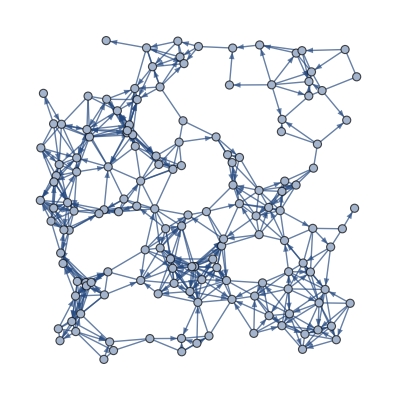
FindPostmanTour[-Graphics-]

```mathematica
FindPostmanTour[UndirectedGraphToMixedGraph[𝒢,.5]]
```

```mathematica
MixedOptimization[g_?GraphQ]:=Block[{u,v,n,m},n=VertexCount[g];m=Transpose[IncidenceMatrix[g]];]
```

## VertexCut

```mathematica
VertexCut[g_?UndirectedGraphQ,parm___]:=VertexCut[DirectedGraph[g],parm]
```

```mathematica
VertexCut[g_?MultigraphQ,parm___]:=VertexCut[SimpleGraph[g],parm]
```

```mathematica
VertexCut[g:Except[_?LoopFreeGraphQ],parm___]:=VertexCut[SimpleGraph[g],parm]
```

```mathematica
VertexCut[g_?DirectedGraphQ]:=
Block[{res,n,m,a,b,u,v},
n=VertexCount[g];
m=Transpose[IncidenceMatrix[g]];
a=UnitStep[m-1];
b=a-m;
res=LinearOptimization[-Total[u+v],{u+v \[VectorLessEqual]1,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

```mathematica
VertexCut[]
```

#### My Attempt

```mathematica
VertexCut[g_?GraphQ]:=
Block[{res,n,m,a,b,u,v},
n=VertexCount[g];
m=Transpose[IncidenceMatrix[g]];
a=UnitStep[m-1];
b=a-m;
res=LinearOptimization[-Total[u+v],{u+v \[VectorLessEqual]1,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

```mathematica
IncidenceMatrix[DirectedGraph@RandomGraph[{12,30}]]//MatrixForm
```

(-1 | -1 | -1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | -1 | -1 | -1)

```mathematica
Clear[𝒢]
```

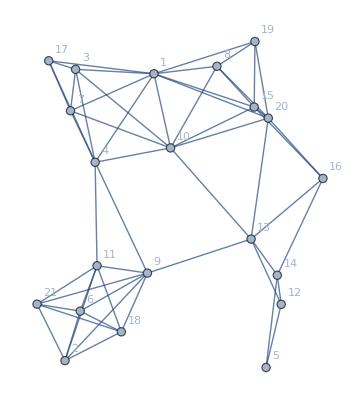

```mathematica
𝒢=Graph[First[TakeLargestBy[ConnectedGraphComponents@RandomGraph[SpatialGraphDistribution[21,E^-1]],EdgeCount,1]],ImageSize->Medium,VertexLabels->"Name"];
𝒢=Graph[𝒢,EdgeWeight->RandomReal[{1,5},EdgeCount[𝒢]]]
```

```mathematica
VertexCut[g_?GraphQ]:=
Block[{res,n,m,a,b,u,v},
n=VertexCount[g];
m=Transpose[IncidenceMatrix[g]];
a=UnitStep[m-1];
b=a-m;
res=LinearOptimization[-Total[u+v],{u+v \[VectorLessEqual]1,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

```mathematica
EdgeWeightedGraphQ[𝒢]
```

True

```mathematica
VertexCount[𝒢]
```

21

```mathematica
WeightedAdjacencyMatrix[𝒢][[1,1]]
```

0

#### Vertex

```mathematica
VertexCut[g_?DirectedGraphQ,s_,t_] /; VertexQ[g,s]&&VertexQ[g,t]:=
Block[{res,n,m,a,b,u,v,i,j},
n=VertexCount[g];
m=Transpose[IncidenceMatrix[g]];
a=UnitStep[m-1];
b=a-m;
i=VertexIndex[g,s];
j=VertexIndex[g,t];
res=LinearOptimization[-Total[u+v],{u+v \[VectorLessEqual]1,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1,Indexed[u,i]==1,Indexed[u,j]==0,Indexed[v,i]==0,Indexed[v,j]==1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

```mathematica
VertexCut[RandomGraph[{5,10}]]
```

LinearOptimization::nsolc: There are no points that satisfy the constraints.

{}